```mathematica
ν[m_][i_][T[i_,j_]]:=(-1)^j qi[m]^-1(
If[j>0,(-1)^(m-i)qi[i+j]T[i+1,j-1],0]+
If[i+j>m/2,qi[2i+j-m/2]T[i+1,j-2],0]+
If[i+j<m/2,qi[j+m/2]T[i+1,j],0]
)
```

```mathematica
ν[m_][i_][a_ t_T]:=a ν[m][i][t]
ν[m_][i_][X_Plus]:=ν[m][i]/@X
```

```mathematica
resμ[m_][i_,z_][T[i_,j_]]:=Sum[
(-1)^i(m-2i)^-1 qi[m]^-1(Sum[ζ[m-2i]^(ℓ(j-jp))(qi[m-i] ζ[m-2i]^-ℓ+(-1)^m qi[i] ζ[m-2i]^ℓ)^-1,{ℓ,0,m-2i-1}])T[i,jp]
,{jp,0,m-2i-1}]
```

```mathematica
resμ[m_][i_,z_][a_ t_T]:=a resμ[m][i,z][t]
resμ[m_][i_,z_][X_Plus]:=resμ[m][i,z]/@X
resμ[m_][i_,z_][X_Times]:=resμ[m][i,z][Expand[X]]
```

```mathematica
X[m_,ω_][0]:=Sum[ω^-j T[0,j],{j,0,m-1}]
```

```mathematica
X[m_,ω_][i_]:=-resμ[m][i,ω][ν[m][i-1][X[m,ω][i-1]]]
```

```mathematica
With[{m=10,ω=-1},
X[m,ω][0]
]
```

T[0,0]-T[0,1]+T[0,2]-T[0,3]+T[0,4]-T[0,5]+T[0,6]-T[0,7]+T[0,8]-T[0,9]

```mathematica
T[0,0]-T[0,1]+T[0,2]-T[0,3]+T[0,4]-T[0,5]+T[0,6]-T[0,7]+T[0,8]-T[0,9]
```

T[0,0]-T[0,1]+T[0,2]-T[0,3]+T[0,4]-T[0,5]+T[0,6]-T[0,7]+T[0,8]-T[0,9]

```mathematica
ζ/:ζ[n_]^m_/;m≥n:=ζ[n]^Mod[m,n]
```

```mathematica
ζ/:ζ[8]^(n_?EvenQ):=ⅈ^(n/2)
ζ/:ζ[8]^(n_?OddQ):=ⅈ^((n-1)/2)ζ[8]
```

```mathematica
qi[k_]:=If[k>0,(q^k-q^-k)/(q-q^-1),0]
```

```mathematica
qi[0]
```

0

```mathematica
qi[4]
```

(-1/q^4+q^4)/(-1/q+q)

```mathematica
a[m_][σ_,ω_]:=Together[X[m,ω][1]/.T[1,j_]:>σ^j]
```

```mathematica
a[10][ⅈ,-1]
```

(2 q^18 (ⅈ+q+ⅈ q^2+q^3+ⅈ q^4+q^5+ⅈ q^6+q^7+ⅈ q^8))/((-ⅈ+q)^4 (ⅈ+q)^4 (1+q^4) (1+ⅈ q-q^2-ⅈ q^3+q^4)^2 (1-ⅈ q-q^2+ⅈ q^3+q^4)^2 (1+q^2+q^4+q^6+q^8)^2)

```mathematica
a[10][ⅈ,1]
```

0

```mathematica
a[10][ⅈ,ⅈ]
```

((1+ⅈ) q^18 (ⅈ+ⅈ q^2+ⅈ q^4+q^5+ⅈ q^6+q^7+ⅈ q^8+ⅈ q^10+ⅈ q^12))/((-ⅈ+q)^4 (ⅈ+q)^4 (1+q^4) (1-q+q^2-q^3+q^4) (1+ⅈ q-q^2-ⅈ q^3+q^4)^3 (1-ⅈ q-q^2+ⅈ q^3+q^4)^3 (1+q+q^2+q^3+q^4)^2)

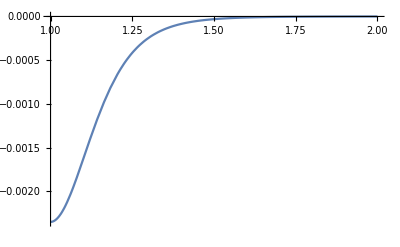

```mathematica
Plot[Evaluate[Re[a[10][ⅈ,Exp[2π ⅈ/8]]]],{q,1,2}]
```

```mathematica
G[n_,σ_,ω_]:=a[2*n+2][σ,ω]*(q^(2*n+2)+q^(-2*n-2)-σ^(2)-σ^(-2)) +Sum[(ω^(-j)+ω^(-j+n+1))*((σ^(j)*qi[2n+2-j]+σ^(j-2)*qi[j])*(-1)^(j)+(σ^(j+1)*qi[n+1-j]+σ^(j-1)*qi[n+1+j])*(-1)^(n+j+1)),{j,0,n}]
```